Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=Import["../data/ccm_manipulated_396096_partitioned_in_time_windows.mx",HeaderLines->1];
```

```mathematica
Print["Weight Zero Rows: ",Length@Position[data[[10]][[All,11]],0]]
Print["Thickness + Width + Length Zero Rows: ",Length@Position[data[[10]][[All,9]],0]]
Print["Usable Rows: ",Length@data[[10]]-Length@Position[data[[10]][[All,9]],0]]
```

Weight Zero Rows: 0

Thickness + Width + Length Zero Rows: 0

Usable Rows: 396096

Investigation of Constraints Impact in Time Windows

```mathematica
GirwanNewmanmodularity[xx_]:=Module[{network,m,Aij,B,u,β,s,Q},
network=xx;
m=EdgeCount@network;
Aij=AdjacencyMatrix@network;
B=N@(Aij-Outer[Times,VertexDegree@network,VertexDegree@network]/(2*m));
u=Eigenvectors@B;
β=Eigenvalues@B;
s=(u/.x_/;x<0->-1)/.x_/;x>0->1;
Q=(Total@(Table[(u[[i]].Flatten@s[[Flatten@Position[β,Max@β]]])^2,{i,VertexList@network}]*β))/(4*m)]
```

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[9,15,10];]
```

{230.982,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep[[1]][[i]],widthdataintimewindowsFixedstep[[2]][[i]],2,7,400,Green],{i,Range@10}];
```

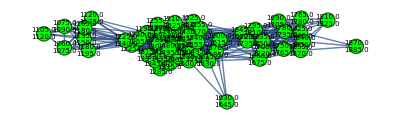
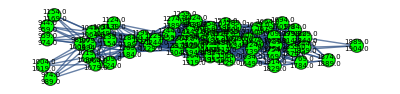
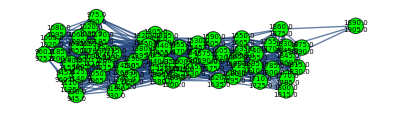
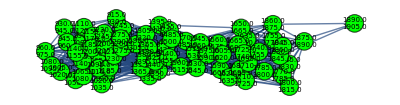
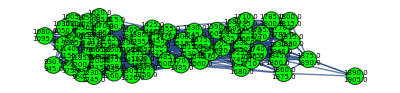
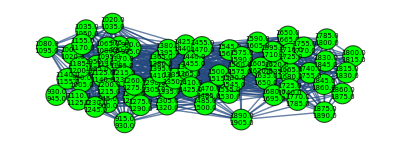
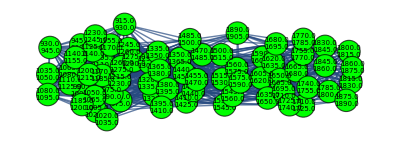
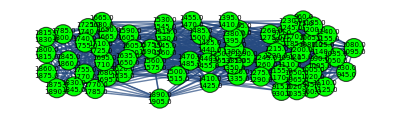
{{-Graphics-,52},{-Graphics-,63},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,66},{-Graphics-,67}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
div1=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β]]],_?Negative];
div2=Flatten@Position[Flatten@s[[Flatten@Position[β,Max@β]]],_?Positive];
Bij=Table[Aij[[i,i]],{i,{div1,div2}}];
(* mg=Total@Table[Total@Bij[[All,i]],{i,Length@Bij}]/2;*)
Bg=Table[N@ReplacePart[Bij[[j]],MapThread[{#1,#1}->#2&,{Range@Length@Bij[[j]],-Table[Total@(Bij[[j]])[[All,i]],{i,Length@Bij[[j]]}]}]],{j,{div1,div2}}];
ug=Table[Eigenvectors@Bg[[i]],{i,{div1,div2}}];
βg=Table[Eigenvalues@Bg[[i]],{i,{div1,div2}}];
sg=Table[(ug[[i]]/.x_/;x<0->-1)/.x_/;x>0->1,{i,{div1,div2}}];
deltaQ=Table[(Total@(Table[((ug[[j]])[[i]].Flatten@(sg[[j]])[[Flatten@Position[βg[[j]],Max@βg[[j]]]]])^2,{i,Length@Bij[[j]]}]*βg[[j]]))/(4*m),{j,{div1,div2}}]
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,2,2,2,2,2,2,3}

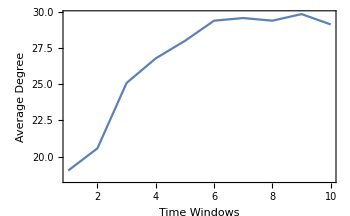
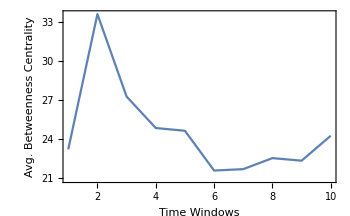
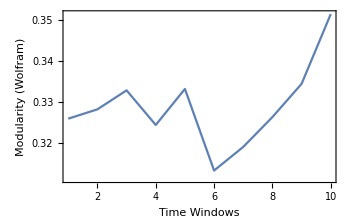
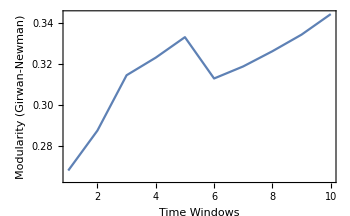

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[10,0.2,10];]
```

{739.618,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep[[1]][[i]],thicknessdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

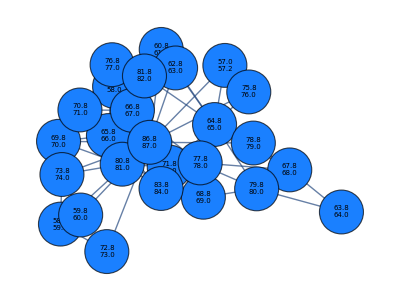
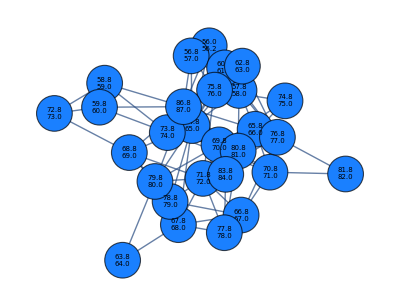
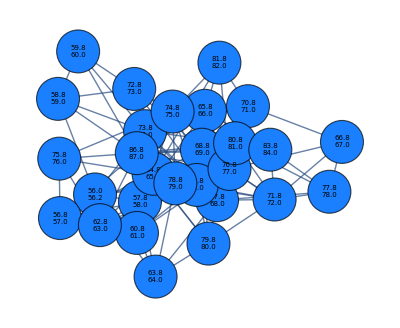
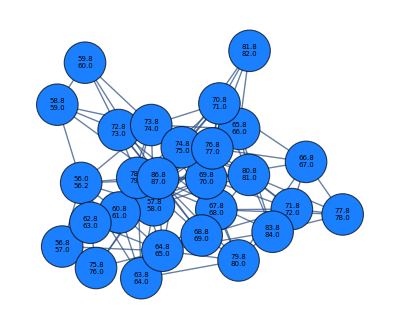
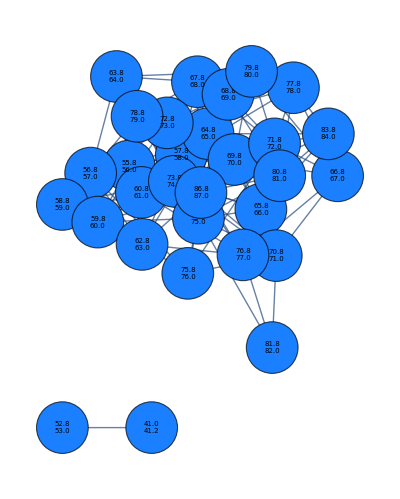
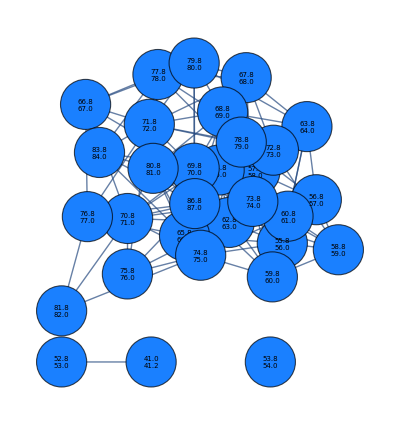
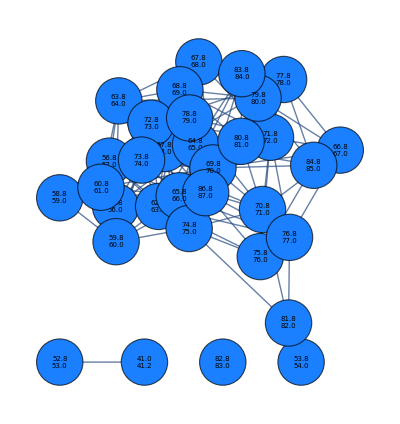
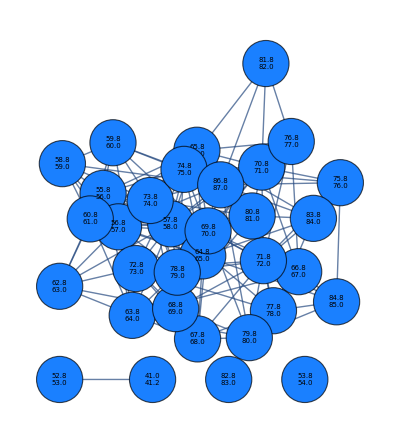
{{-Graphics-,26},{-Graphics-,28},{-Graphics-,28},{-Graphics-,28},{-Graphics-,30},{-Graphics-,31},{-Graphics-,33},{-Graphics-,33},{-Graphics-,35},{-Graphics-,35}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{4,4,4,4,4,4,6,5,5,4}

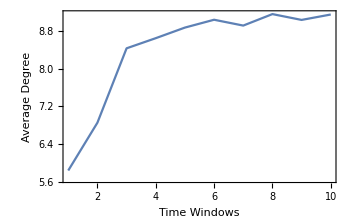
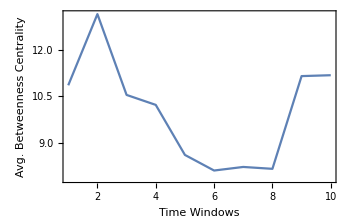
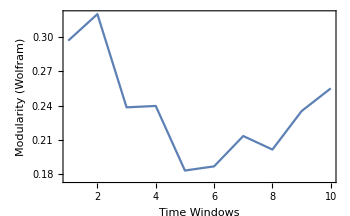
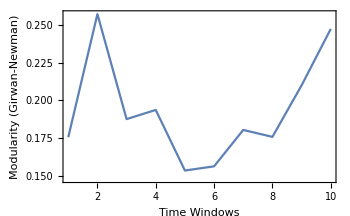

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[12,600,10];]
```

{229.445,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedstep[[1]][[i]],lengthdataintimewindowsFixedstep[[2]][[i]],2,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

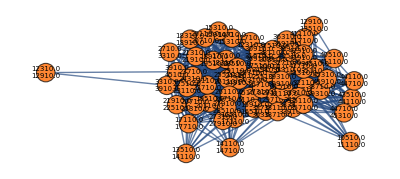
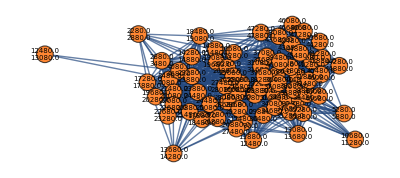
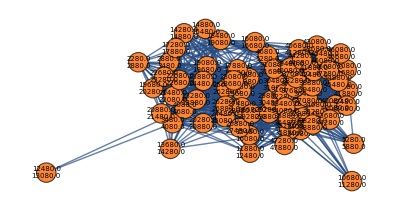
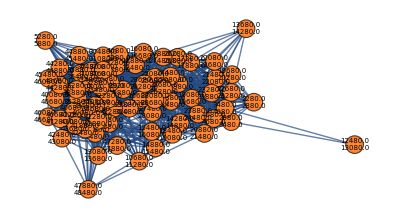
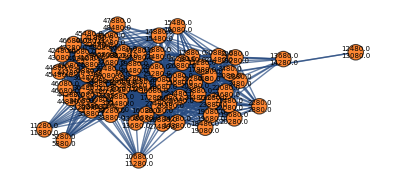
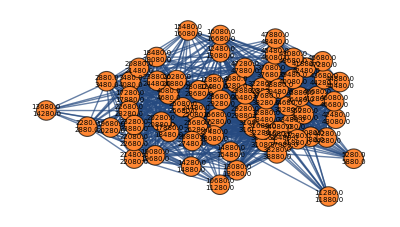
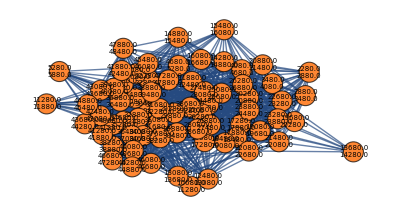
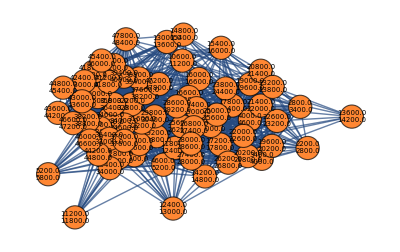
{{-Graphics-,61},{-Graphics-,67},{-Graphics-,67},{-Graphics-,68},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,69},{-Graphics-,70},{-Graphics-,70}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

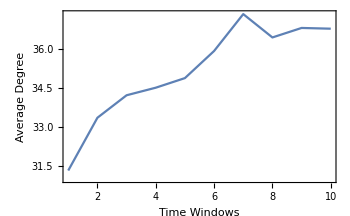
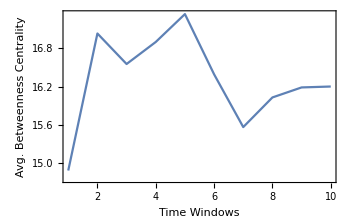
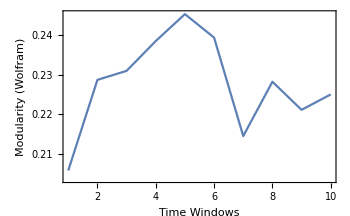
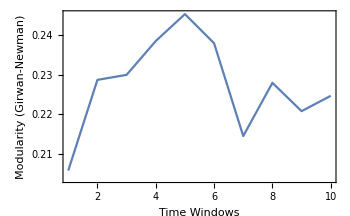

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedstep=snetworkdatabinnedintimewindows[11,600,10];]
```

{164.225,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedstep[[1]][[i]],weightdataintimewindowsFixedstep[[2]][[i]],2,7,400,Red],{i,Range@10}];
```

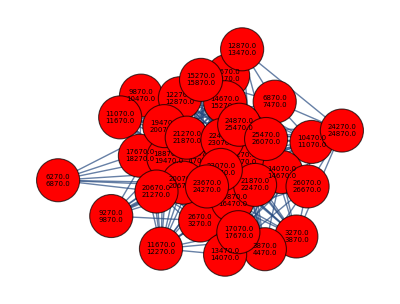
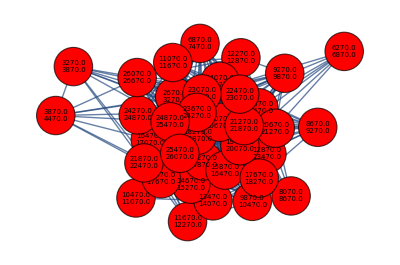
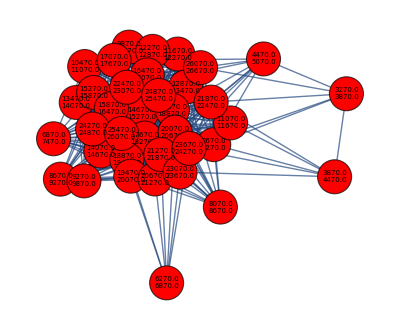
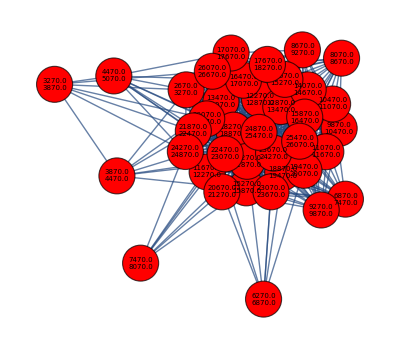
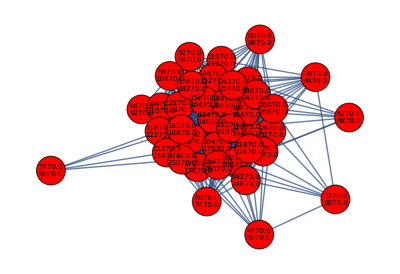
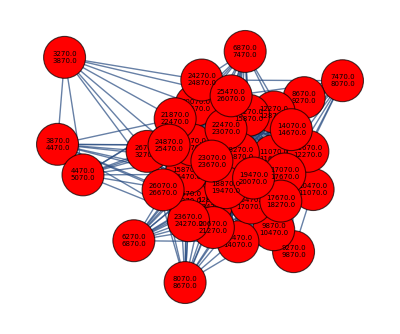
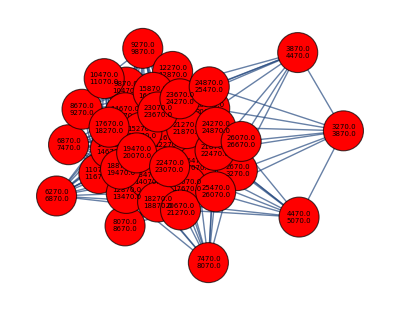
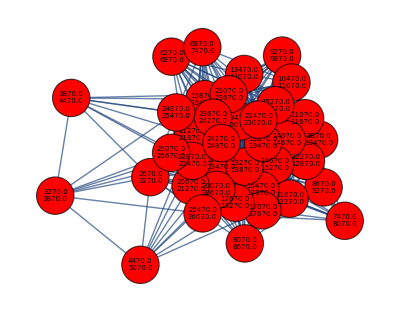
{{-Graphics-,35},{-Graphics-,36},{-Graphics-,37},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,3,3,3,2,2,2,2,2,2}

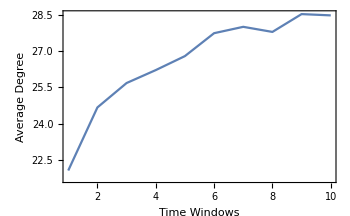
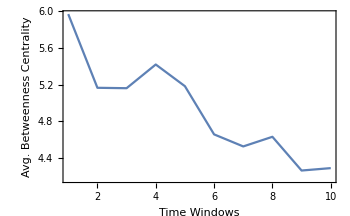
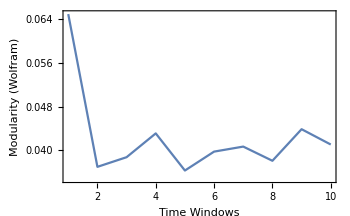
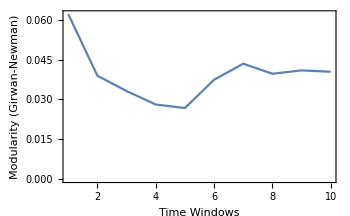

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[9,60,10];]
```

{1813.06,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket[[1]][[i]],widthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Green],{i,Range@10}];
```

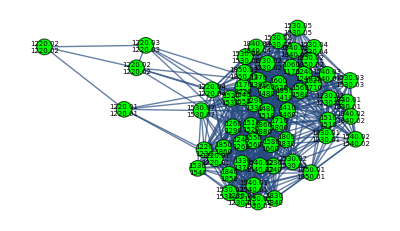
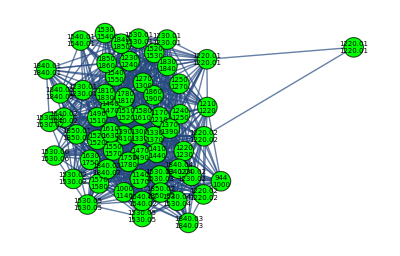
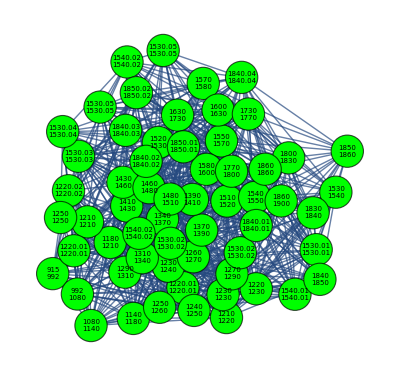
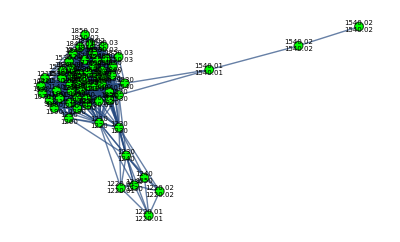
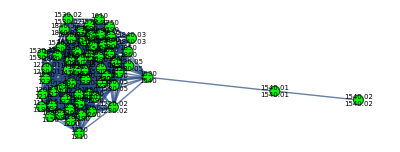
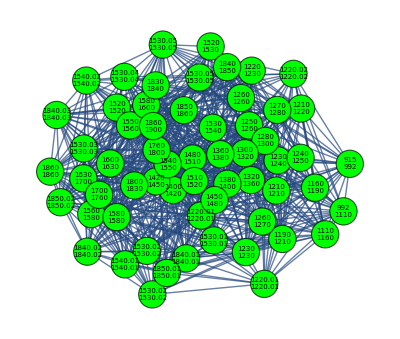
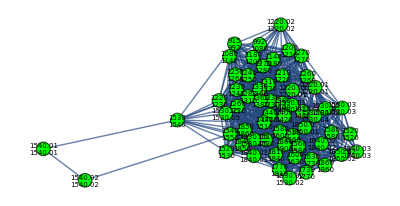
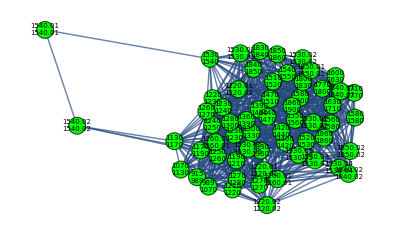
{{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60},{-Graphics-,60}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,3,2,3,3,2,2,3,2,2}

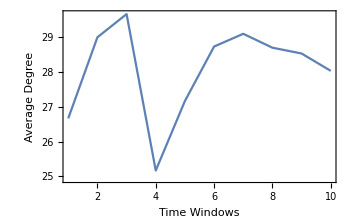
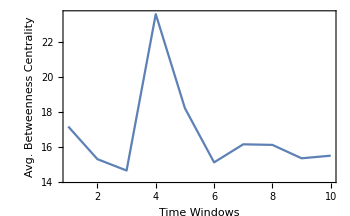
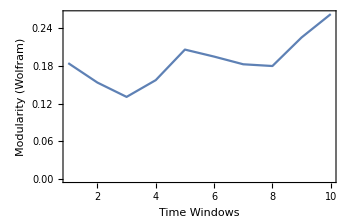
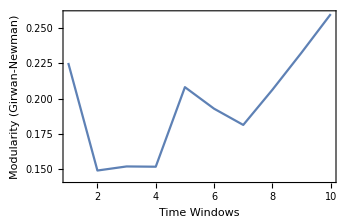

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[10,32,10];]
```

{2939.01,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket[[1]][[i]],thicknessdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@10}];
```

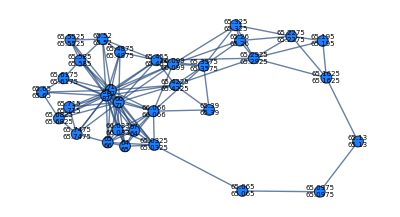
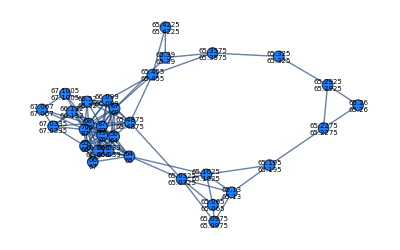
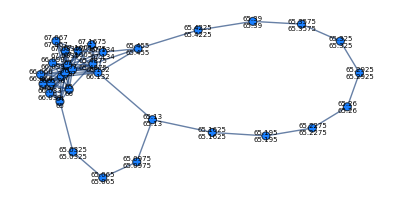
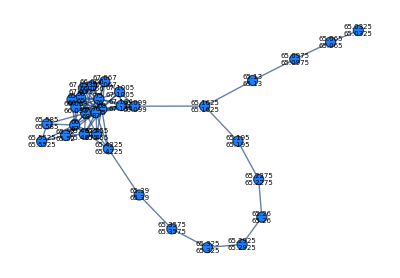
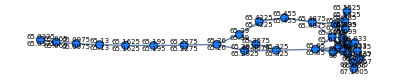
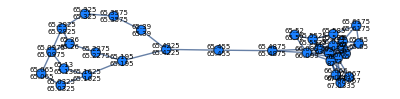
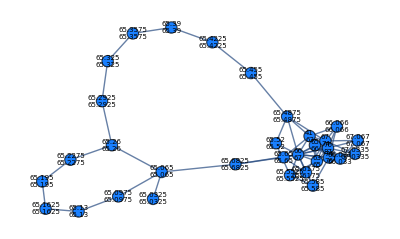
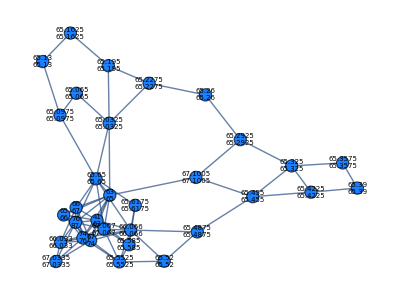
{{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32},{-Graphics-,32}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{3,4,3,4,4,4,4,4,4,4}

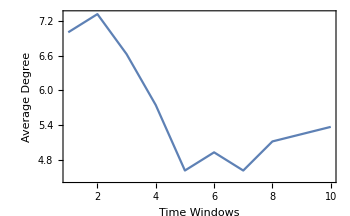
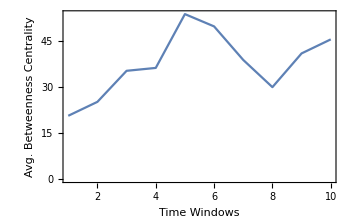
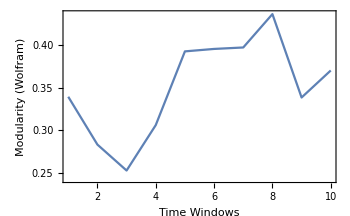
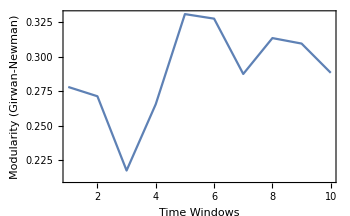

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Length Feature

```mathematica
AbsoluteTiming[lengthdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[12,65,10];]
```

{917.129,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[lengthdataintimewindowsFixedbucket[[1]][[i]],lengthdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,RGBColor[1.,0.53,0.2]],{i,Range@10}];
```

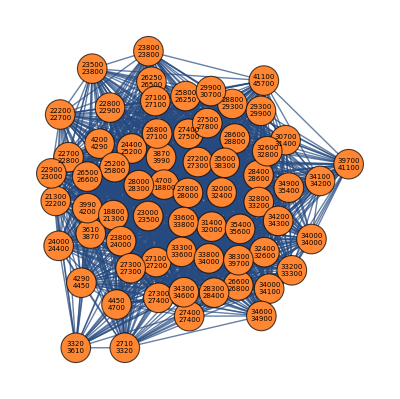
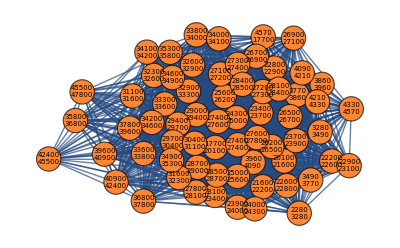
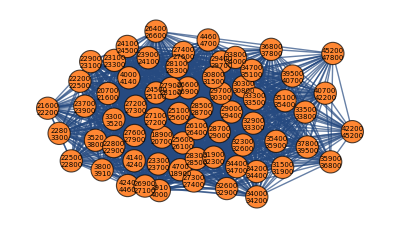
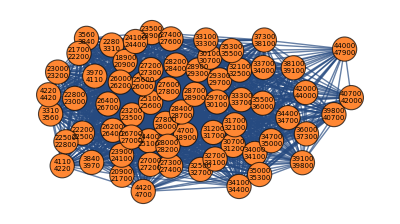
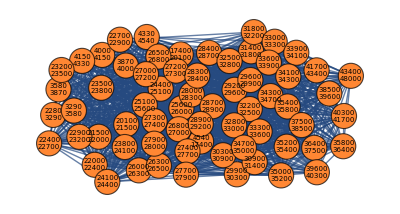
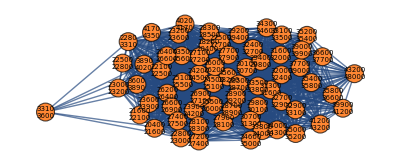
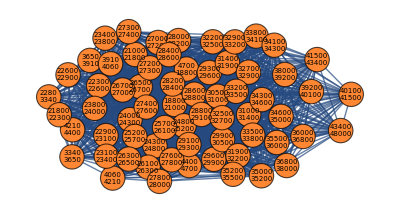
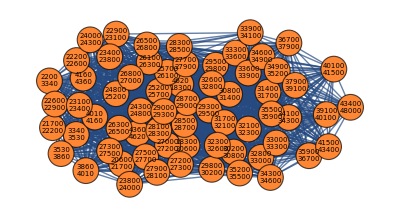
{{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65},{-Graphics-,65}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

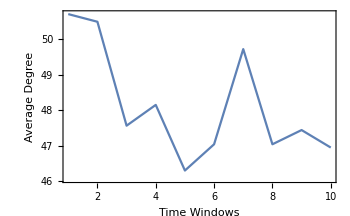
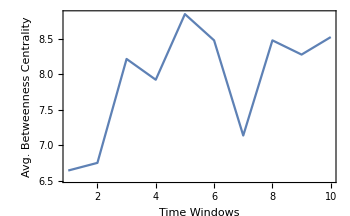
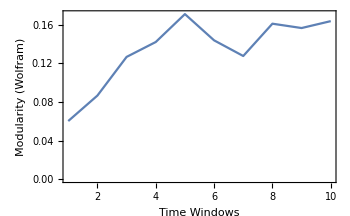
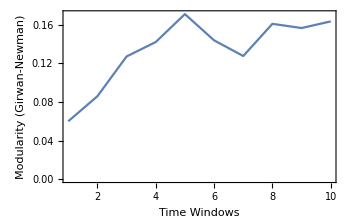

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```

Weight Feature

```mathematica
AbsoluteTiming[weightdataintimewindowsFixedbucket=snetworkdatafxdbucketintimewindows[11,38,10];]
```

{2015.52,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[weightdataintimewindowsFixedbucket[[1]][[i]],weightdataintimewindowsFixedbucket[[2]][[i]],1.5,7,400,Red],{i,Range@10}];
```

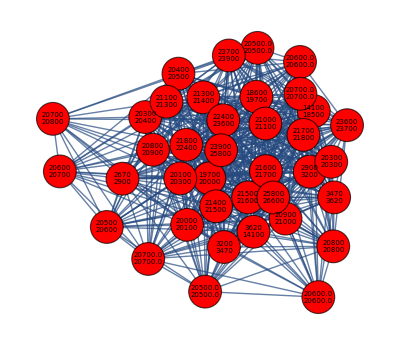
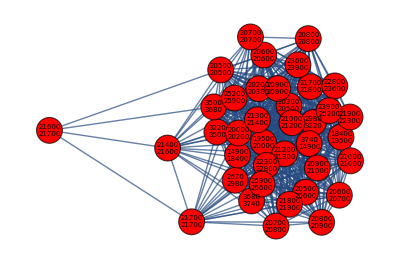
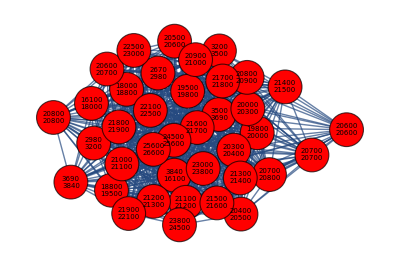
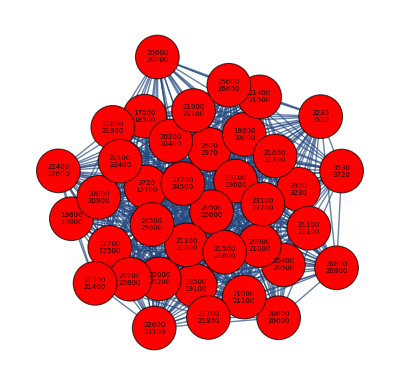
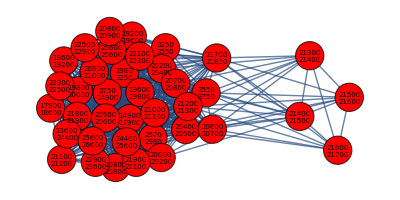
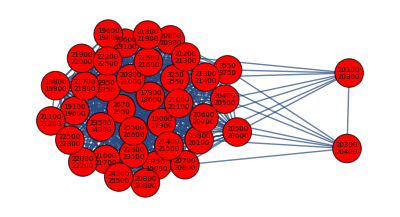
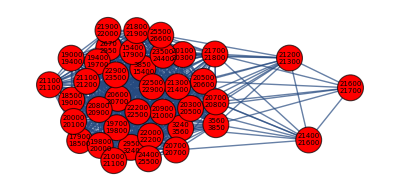
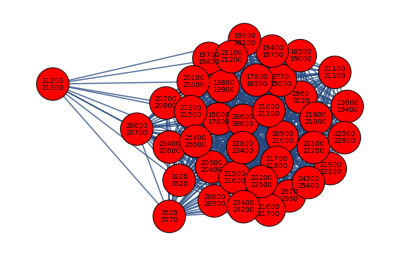
{{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38},{-Graphics-,38}}

```mathematica
graphsandnodenumbers
```

```mathematica
ABCvalues=Table[Mean@BetweennessCentrality[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
modularityvalues=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
degreevalues=Table[N@Mean@VertexDegree[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
GNmodularityvalues=Table[GirwanNewmanmodularity[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}];
```

```mathematica
Table[Length@FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],{i,Length@graphsandnodenumbers}]
```

{2,2,2,2,2,2,2,2,2,2}

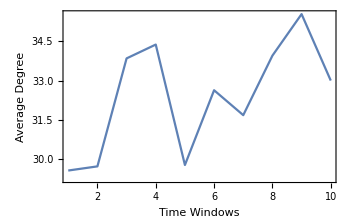
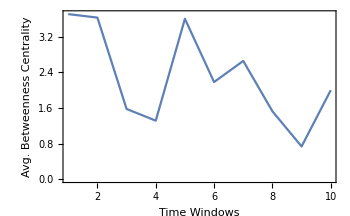
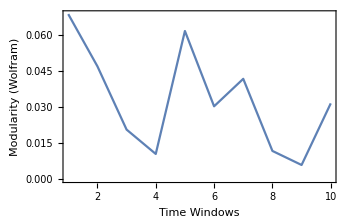
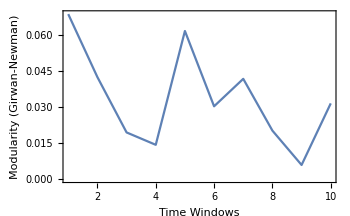

```mathematica
{ListLinePlot[Thread[{Range@10,degreevalues}],Frame->True,FrameLabel->{"Time Windows","Average Degree"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,ABCvalues}],Frame->True,FrameLabel->{"Time Windows","Avg. Betweenness Centrality"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,modularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Wolfram)"},ImageSize->350,PlotRange->{{1,10},All}],ListLinePlot[Thread[{Range@10,GNmodularityvalues}],Frame->True,FrameLabel->{"Time Windows","Modularity (Girwan-Newman)"},ImageSize->350,PlotRange->{{1,10},All}]}
```